```mathematica
G[u_,v_,J_,K_]:= (2 u K)/(v-u +v J +u K+√((v-u+v J+u K)^2-4(v-u)u  K))(*Goldbeter-Koshland Function*)
```

```mathematica
sys1:= D[X[t],t]== k5  R[t]- k6 X[t](*the pdes *)
sys2:= D[R[t],t]==k0 G[k3 R[t],k4,J3,J4]+k1 S -k2 R[t] -K2 X[t] R[t]
￼


param:={k0->4 , k1->1 , k2-> 1,k3->1,K2-> 1,k4-> 1,k5-> 0.1 ,k6-> 0.075 , J3-> 0.3,J4-> 0.3,S->0.2};(*parameters*)
```

￼

￼

```mathematica
w1=Solve[sys1[[2]]==0/.param, R[t]];(*nullclines of dX/dt*)
p2=Plot[Evaluate[{R[t]/.w1[[1]]}],{X[t],0,3},PlotRange->{{0,1.5},{0,3}},PlotRangeClipping->True,Frame->True,PlotStyle->Blue,FrameLabel->{"X","R"}];
```

```mathematica
a1=Solve[sys2[[2]]==0/.param, R[t]];(*nullclines of dR/dt, gives three soluion*)
p11=Plot[Evaluate[{R[t]/.a1[[1]]}],{X[t],0,3},PlotRange->{{0,1.5},{0,3}},PlotRangeClipping->True,Frame->True,PlotStyle->{Red,Dashed},FrameLabel->{"X","R"}];
p12=Plot[Evaluate[{R[t]/.a1[[2]]}],{X[t],0,3},PlotRange->{{0,1.5},{0,3}},PlotRangeClipping->True,Frame->True,PlotStyle->{Red}];
p13=Plot[Evaluate[{R[t]/.a1[[3]]}],{X[t],0,3},PlotRange->{{0,1.5},{0,3}},PlotRangeClipping->True,Frame->True,PlotStyle->{Red}];
```

```mathematica
var={R,X};(*variables for numerical solution*)
```

```mathematica
r=NDSolve[{sys1,sys2,X[0]==0.1,R[0]==0}/. param,var,{t,0,500}];(*numericall soultion to systems of pdes*)
```

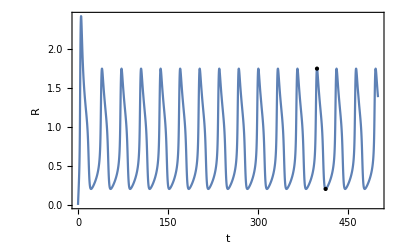

```mathematica
min= FindMinimum[(R[t]/.r)⟦1⟧,{t,400,500}];(*trail for finding maximum and minimum values *)
max=FindMaximum[(R[t]/.r)⟦1⟧,{t,400,500}];

pt1=Reverse[Cases[min,_?NumberQ,Infinity]];
pt2=Reverse[Cases[max,_?NumberQ,Infinity]];
pl4=Plot[(R[t]/.r)⟦1⟧,{t,0,500},Epilog->{PointSize[Medium],{Point[pt2],Point[pt1]}},Frame->True,FrameLabel->{"t","R"},LabelStyle->{GrayLevel[0],Bold}]
```

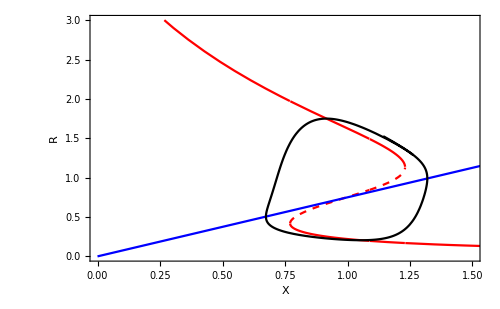

```mathematica
pl5=ParametricPlot[{(X[t]/.r)[[1]],(R[t]/.r)[[1]]},{t,10,45},Frame->True,PlotRange->{{0,1.5},{0,3}},PlotRangeClipping->True, PlotStyle->Black];(*the phase plot for the closed orbit*)
Show[{p11,p12,p13,p2,pl5},FrameLabel->{"X","R"},LabelStyle->{GrayLevel[0],Bold}]
```

```mathematica
StX= Solve[sys1[[2]]==0, X[t]];(*solving for signal response curve*)
```

```mathematica
param1:={k0->4 , k1->1 , k2-> 1,k3->1,K2-> 1,k4-> 1,k5-> 0.1 ,k6-> 0.075 , J3-> 0.3,J4-> 0.3}(*parameters*)
sys3= sys2/. StX[[1]];(*substituting the X[t]*)
```

```mathematica
b1=Solve[sys3[[2]]==0/.param1, R[t]];(*steady state solution*)
```

```mathematica
pp1=Plot[Evaluate[{R[t]/.b1[[3]]}],{S,0,0.5},PlotRange->{{0,0.5},{0,2}},PlotRangeClipping->True,Frame->True,Mesh->{{0.06,0.42}},MeshShading->{{},Dashed}];(*the signal response curve *)
```

```mathematica
StablePoints[SS_]:=(*function that takes S and gives the maximum and minimum points *)
Module[{tmp1,tmp2,tmp3},
tmp1=NDSolve[{sys1,sys2,X[0]==0.5,R[0]==0.5}/. param1 /.S-> SS ,var,{t,0,500}];
tmp2=FindMinimum[(R[t]/.tmp1)⟦1⟧,{t,400,500}][[1]];(*maximum and minmimum points at stable point for large t*)
tmp3=FindMaximum[(R[t]/.tmp1)⟦1⟧,{t,400,500}][[1]];
Return[{{SS,tmp2},{SS,tmp3}}]]
```

```mathematica
Points=Flatten[Table[StablePoints[SS],{SS,0.04,0.42,0.01}],1];(*maximum and minimum points for the range *)
```

InterpolatingFunction::dmval: Input value {513.212} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1175.67} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1655.06} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {1175.67} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {513.212} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-79.575} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {513.418} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {538.489} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {583.515} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dprec: The precision of input value {8.66451×10^17} and/or the interpolation grid is insufficient to compute the value.

FindMaximum::nrnum: The function value -«1» is not a real number at {t} = {8.66451×10^17}.

InterpolatingFunction::dprec: The precision of input value {7.46301×10^17} and/or the interpolation grid is insufficient to compute the value.

FindMinimum::nrnum: The function value «1» is not a real number at {t} = {7.46301×10^17}.

InterpolatingFunction::dprec: The precision of input value {5.836×10^17} and/or the interpolation grid is insufficient to compute the value.

General::stop: Further output of InterpolatingFunction::dprec will be suppressed during this calculation.

FindMaximum::nrnum: The function value -«1»[5.836×10^17] is not a real number at {t} = {5.836×10^17}.

General::stop: Further output of FindMaximum::nrnum will be suppressed during this calculation.

General::stop: Further output of FindMinimum::nrnum will be suppressed during this calculation.

```mathematica
ll1=ListPlot[Points,PlotRange->{{0,0.5},{0,2}},PlotRangeClipping->True,Frame->True,PlotStyle->{Thick,Black}];(*list plots *)
```

ListPlot::lpn: Points is not a list of numbers or pairs of numbers.

```mathematica
Points1=Flatten[Table[StablePoints[SS],{SS,0.4,0.42,0.001}],1];(*maximum and minimum points for the range *)
```

```mathematica
ll2=ListPlot[Points1,PlotRange->{{0,0.5},{0,2}},PlotRangeClipping->True,Frame->True,PlotStyle->{Thick,Black}];
```

```mathematica
Show[{pp1,ll1,ll2},FrameLabel->{"Signal(S)","Response(R)"},LabelStyle->{GrayLevel[0],Bold}]
```

-Graphics-